## Function Definitions

```mathematica
lowLim=1*^3; (* eV *)
uplim=1*^9; (* eV *)

a0=5.29*10^-11; (* m *)
R=13.6; (* eV *)
α=1/137.;
eRestMass=0.511*^6; (* eV *)
lightspeed=3*^8; (* m/s *)
a=0.3;
b=0.7;
```

```mathematica
t[T_,B_]:=T/B;
S[B_,nocc_]:=4π a0^2 nocc(R/B)^2;
Cf[z1eff_,z2eff_,n1_,n2_]:=a z1eff^2/(2 n1^2)+b z2eff^2/(2 n2^2);
c[B_,z1eff_,z2eff_,n1_,n2_]:=(Cf[z1eff,z2eff,n1,n2]/B)2 R;
```

```mathematica
σ[T_,B_,z1eff_,z2eff_,n1_,n2_,nocc_]:=Piecewise[{{0.,T/B<1},{S[B,nocc]/(t[T,B]+c[B,z1eff,z2eff,n1,n2])(1/2(1-1/t[T,B]^2)Log[t[T,B]]+(1-1/t[T,B])-Log[t[T,B]]/(t[T,B]+1)),T/B≥1}}];
```

```mathematica
tprime[T_]:=T/eRestMass;
bprime[B_]:=B/eRestMass;
betaT2[T_]:=1-1/(1+tprime[T])^2;
betaB2[B_]:=1-1/(1+bprime[B])^2;
```

```mathematica
σrel[T_,B_,z1eff_,z2eff_,n1_,n2_,nocc_]:=Piecewise[{{0.,T/B<1},{(4π a0^2 α^4 nocc)/((betaT2[T]+c[B,z1eff,z2eff,n1,n2]betaB2[B])2bprime[B])(1/2(Log[betaT2[T]/(1-betaT2[T])]-betaT2[T]-Log[2bprime[B]])(1-1/t[T,B]^2)+1-1/t[T,B]-Log[t[T,B]]/(t[T,B]+1)(1+2tprime[T])/(1+tprime[T]/2)^2+bprime[B]^2/(1+tprime[T]/2)^2(t[T,B]-1)/2),T/B≥1}}];
```

## Test Calculation Against Paper

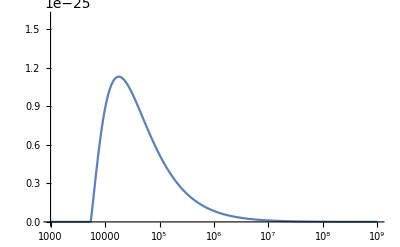

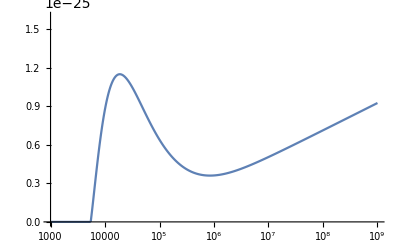

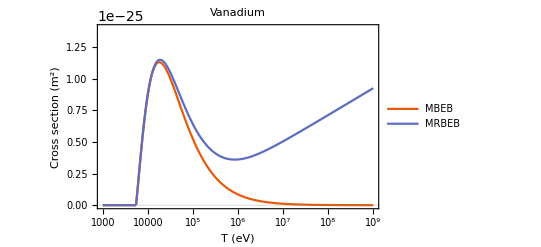

```mathematica
(*LogLinearPlot[t[en,Bind],{en,lowLim,uplim},PlotRange->All]
LogLinearPlot[S[en],{en,lowLim,uplim},PlotRange->All]
LogLinearPlot[c[en,6],{en,lowLim,uplim},PlotRange->All]*)
z1eff=22.4256;
n1=1;
z2eff=8.0907;
n2=2;

Bind=5463.76; (* eV *)
Z=23;
nocc=2;
LogLinearPlot[σ[en,Bind,z1eff,z2eff,n1,n2,nocc],{en,lowLim,uplim},PlotRange->{0.,1600*^-28},PlotPoints->500]
LogLinearPlot[σrel[en,Bind,z1eff,z2eff,n1,n2,nocc],{en,lowLim,uplim},PlotRange->{0.,1600*^-28},PlotPoints->500]
LogLinearPlot[{σ[en,Bind,z1eff,z2eff,n1,n2,nocc],σrel[en,Bind,z1eff,z2eff,n1,n2,nocc]},{en,lowLim,uplim},PlotRange->{0.,1400*^-28},PlotPoints->500, PlotTheme->"Scientific",PlotLegends->{"MBEB","MRBEB"},PlotLabel->"Vanadium",FrameLabel->{"T (eV)","Cross section (m^2)"},LabelStyle->{18}]
```

## Calculate Total Cross Sections

```mathematica
(*18 Ar: 3.2060, 0.3263, 0.2507, 0.2486, 0.0292, 0.0159, 0.0158*)
(*8 O: 0.5320, 0.0285, 0.0071, 0.0071*)
(*7 N: 0.4016, 0.0244, 0.0092, 0.0092*)
```

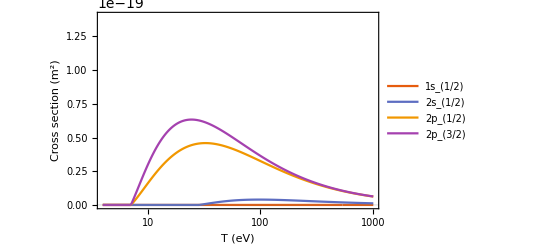

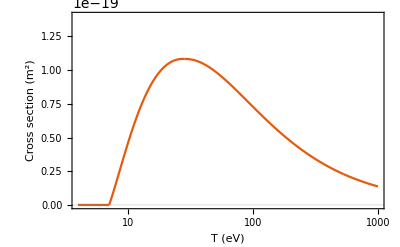

```mathematica
(*O*)
(*1s1/2 -> 2s1/2*)
z1eff=7.6579;
n1=1;
z2eff=2.2458;
n2=2;
Bind=0.5320*1000.; (* eV *)
nocc=2;
o1s=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*2s1/2 -> 2p1/2*)
z1eff=2.2458;
n1=2;
z2eff=2.2266;
n2=2;
Bind=0.0285*1000.; (* eV *)
nocc=2;
o2s=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*2p1/2 -> 2p3/2*)
z1eff=2.2266;
n1=2;
z2eff=2.2266;
n2=2;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p12=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*2p3/2*)
z1eff=2.2458;
n1=2;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p32=Piecewise[{{0.,en/Bind<1},{(4π a0^2 α^4 nocc)/((betaT2[en]+z1eff^2/(2 n1^2) betaB2[Bind])2bprime[Bind])(1/2(Log[betaT2[en]/(1-betaT2[en])]-betaT2[en]-Log[2bprime[Bind]])(1-1/t[en,Bind]^2)+1-1/t[en,Bind]-Log[t[en,Bind]]/(t[en,Bind]+1)(1+2tprime[en])/(1+tprime[en]/2)^2+bprime[Bind]^2/(1+tprime[en]/2)^2(t[en,Bind]-1)/2),en/Bind≥1}}];
LogLinearPlot[{o1s,o2s,o2p12,o2p32},{en,4,1000},PlotRange->{0.,1.4*^-19},PlotPoints->500,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
LogLinearPlot[o1s+o2s+o2p12+o2p32,{en,4,1000},PlotRange->{0.,1.4*^-19},PlotPoints->500,PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
```

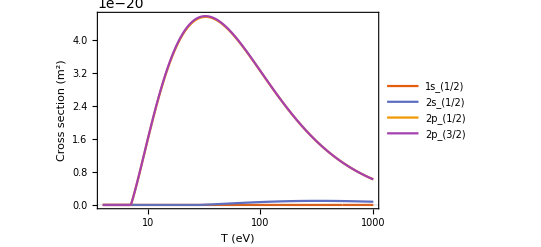

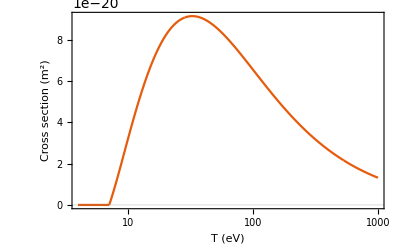

```mathematica
(*O*)
(*2p3/2 -> 2p1/2*)
z1eff=2.2266;
n1=2;
z2eff=2.2266;
n2=2;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p32=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*2p1/2 -> 2s1/2*)
z1eff=2.2266;
n1=2;
z2eff=2.2458;
n2=2;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p12=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*2s1/2 -> 1s1/2*)
z1eff=2.2458;
n1=2;
z2eff=7.6579;
n2=1;
Bind=0.0285*1000.; (* eV *)
nocc=2;
o2s=σrel[en,Bind,z1eff,z2eff,n1,n2,nocc];

(*1s1/2*)
z1eff=7.6579;
n1=1;
Bind=0.5320*1000.; (* eV *)
nocc=2;
o1s=Piecewise[{{0.,en/Bind<1},{(4π a0^2 α^4 nocc)/((betaT2[en]+z1eff^2/(2 n1^2) betaB2[Bind])2bprime[Bind])(1/2(Log[betaT2[en]/(1-betaT2[en])]-betaT2[en]-Log[2bprime[Bind]])(1-1/t[en,Bind]^2)+1-1/t[en,Bind]-Log[t[en,Bind]]/(t[en,Bind]+1)(1+2tprime[en])/(1+tprime[en]/2)^2+bprime[Bind]^2/(1+tprime[en]/2)^2(t[en,Bind]-1)/2),en/Bind≥1}}];
LogLinearPlot[{o1s,o2s,o2p12,o2p32},{en,4,1000},PlotRange->All,PlotPoints->500,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
LogLinearPlot[o1s+o2s+o2p12+o2p32,{en,4,1000},PlotRange->All,PlotTheme->"Scientific",PlotPoints->500,FrameLabel->{"T (eV)","Cross section (m^2)"}]
```